## prel

```mathematica
$PrePrint=#/. {Csc[z_]:>1/Defer@Sin[z],Sec[z_]:>1/Defer@Cos[z]}&;
rep={kx->k Sin[θ] Cos[ϕ],ky->k Sin[θ] Sin[ϕ],kz->k Cos[θ]};
ass=Assumptions->{kx,ky,kz,k,θ,c,v0,ϕ,θp,ϕp,kf,μ,s} ∈ Reals && k>0 && kf>0 && 0<=θ<=π && 0<=θp<=π && c>0 && v0>0 && μ>0;
repl={kx->kf Sin[θ] Cos[ϕ],ky->kf Sin[θ] Sin[ϕ],kz->kf Cos[θ]};
srep={kf->kf1[θ],(s v0)/(√(kf1[θ]^2))->(s v0)/kf1[θ]};
```

## Fermi surfaces

```mathematica
Solve[k ( c k+s v0)==μ,k]/.s^2->1
```

{{k→(-s v0-√(v0^2+4 c μ))/(2 c)},{k→(-s v0+√(v0^2+4 c μ))/(2 c)}}

{{k→μ/(s v0)}}

```mathematica
(Flatten[Simplify[SolveValues[c k^2+s v0 k ==μeff,k],ass]/.{s^3->s,s^2->1},1])/.μeff->μ-s B mbohr
```

{-(s v0+√(v0^2+4 c (-B mbohr s+μ)))/(2 c),(-s v0+√(v0^2+4 c (-B mbohr s+μ)))/(2 c)}

## sigma

```mathematica
Clear[sign,s,c,μ,B,v0];
sign[B_,μ_,c_,v0_,{βintra_,βinter_},mbohr_,om_]:=Block[{e=1,kf1vec,kf2vec,matr,bc1,bc2,θ,τ1,τ2,kf1,ϕ=0,kf2,f1,f2,vvec1,vvec2,vmm1,vmm2,vdotk1,vdotk2,conteq,λ1,λ2,a1,a2,cost,θp,s,Dphase1,Dphase2,h1,vz1,h2,vz2,zero1,zero2,ct1,ct2,ctct1,cs,ctct2,hzero1,hzero2,hct1,hct2,hstcp1,hstcp2,hstsp1,hstsp2,colvec,mat,sol,sol1,Λ1,Λ2,s1,s2,int1,int2},
(* band 1 *)
s=1;
kf1[θ_]=(-s v0+√(v0^2+4 c (-B mbohr s+μ)))/(2 c);
bc1[θ_]=(-s om)/(2 ( kf1[θ])^2){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase1[θ_]=1 +e {0,0,B}.bc1[θ] (*-Graphics-*);
vvec1[θ_]= (2 c kf1[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm1[θ_]={0,0,0};
vdotk1[θ_]=s v0 kf1[θ]+2 c kf1[θ]^2;
(* -Graphics-*)
h1[θ_]=1/Dphase1[θ]( (vvec1[θ]+vmm1[θ])[[3]]+ e B(bc1[θ].(vvec1[θ]+vmm1[θ])) );
(*****************)

(* band 2 *)
s=-1;
kf2[θ_]=(-s v0+√(v0^2+4 c (-B mbohr s+μ)))/(2 c);
bc2[θ_]=(-s om)/(2 ( kf2[θ])^2){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
Dphase2[θ_]=1 +e {0,0,B}.bc2[θ] (*-Graphics-*);
vvec2[θ_]= (2 c kf2[θ]+s v0){ Sin[θ]Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]};
vmm2[θ_]={0,0,0};
vdotk2[θ_]=s v0 kf2[θ]+2 c kf2[θ]^2;
h2[θ_]=1/Dphase2[θ]( (vvec2[θ]+vmm2[θ])[[3]]+ e B(bc2[θ].(vvec2[θ]+vmm2[θ])));
(*****************)
(* -Graphics- *)
τ1[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}]+βinter/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]+(- βinter Cos[θ])/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}])^-1;
(**************)
τ2[θ_]=(βintra/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]+
(βintra   Cos[θ])/2 NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}]+βinter/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+(- βinter Cos[θ])/2 NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}])^-1;

(******************)
f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ct2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctct2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];

hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hzero2=Quiet[NIntegrate [f2[θp]h2[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hct2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];

colvec=({{1/2 (hzero2 βinter+hzero1 βintra)}, {1/2 (-hct2 βinter+hct1 βintra)}, {1/2 (hzero1 βinter+hzero2 βintra)}, {1/2 (-hct1 βinter+hct2 βintra)}});
mat=({{1-(zero1 βintra)/2, -(ct1 βintra)/2, -(zero2 βinter)/2, -(ct2 βinter)/2}, {-(ct1 βintra)/2, 1-(ctct1 βintra)/2, (ct2 βinter)/2, (ctct2 βinter)/2}, {-(zero1 βinter)/2, -(ct1 βinter)/2, 1-(zero2 βintra)/2, -(ct2 βintra)/2}, {(ct1 βinter)/2, (ctct1 βinter)/2, -(ct2 βintra)/2, 1-(ctct2 βintra)/2}});
matr=mat.{λ1,a1,λ2,a2};
cs=λ1 zero1-hzero1+a1 ct1+λ2 zero2-hzero2+a2 ct2;
sol=Flatten[Solve[{matr[[1]]+colvec[[1]]==0,matr[[3]]+colvec[[3]]==0,matr[[4]]+colvec[[4]]==0,cs==0},{λ1,a1,λ2,a2}],1];
Λ1[θ_]=(λ1-h1[θ]+a1 Cos[θ])/.sol;
int1[θ_]=-f1[θ]h1[θ]Λ1[θ];
s1=NIntegrate[int1[θ],{θ,0,π}];

Λ2[θ_]=(λ2-h2[θ]+a2 Cos[θ])/.sol;
int2[θ_]=-f2[θ]h2[θ]Λ2[θ];
s2=NIntegrate[int2[θ],{θ,0,π}];
{B,s1,s2}
];
(* sig[B_,μ_,c_,v0_,{βintra_,βinter_},mbohr_,om_] *)
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
sign[1,mu,cval,v0val,{in,0.5 in}, bohrrm,omval]
```

{1,0.0000930583,0.000107192}

## test

```mathematica
mu=10.0^-0; cval=5 10^-4 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;rat=0.4;
dat=Table[sign[B,mu,cval,v0val,{1,10^4}, bohrrm,omval],{B,-55,55,10}]
```

{{-55,9.34601×10^-8,1.06869×10^-7},{-45,9.34566×10^-8,1.06868×10^-7},{-35,9.34536×10^-8,1.06867×10^-7},{-25,9.34512×10^-8,1.06867×10^-7},{-15,9.34493×10^-8,1.06867×10^-7},{-5,9.34479×10^-8,1.06867×10^-7},{5,9.3447×10^-8,1.06868×10^-7},{15,9.34467×10^-8,1.0687×10^-7},{25,9.34469×10^-8,1.06871×10^-7},{35,9.34476×10^-8,1.06873×10^-7},{45,9.34488×10^-8,1.06876×10^-7},{55,9.34506×10^-8,1.06879×10^-7}}

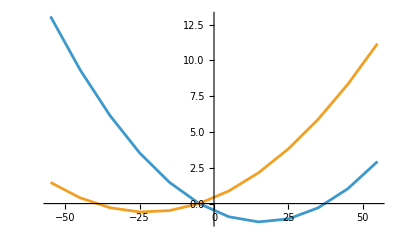

```mathematica
list=dat;
len=Length[list];
x=1/list[[6,2]];
d1at11=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^5},{i,1,len}];
x=1/list[[6,3]];
d1at12=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^5},{i,1,len}];
ListLinePlot[{d1at11,d1at12}]
```

## Results

### set 1

```mathematica
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;rat=0.5;
dat=Table[sign[B,mu,cval,v0val,{in,rat in}, bohrrm,omval],{B,-105,105,10}]
```

sig0[1.,1/20000,1/2000,{1,0.5}]

```mathematica
Quiet[sig0[mu,cval,v0val,{in,rat in}]]//Chop
```

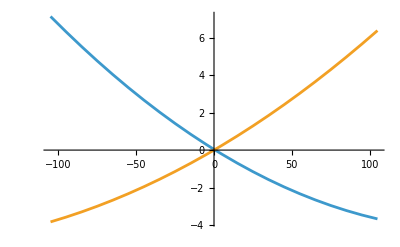

```mathematica
list=Sort[{{0,0.00009305833645251493,0.00010719166354748506},{-105,0.00009306492860365777,0.0001071875603632772},{-95,0.00009306416541099842,0.00010718783372872941},{-85,0.00009306343071663562,0.00010718813181334132},{-75,0.00009306272452064034,0.00010718845461696783},{-65,0.0000930620468232599,0.00010718880213944003},{-55,0.00009306139762455215,0.00010718917438062088},{-45,0.00009306077692465084,0.00010718957134036434},{-35,0.00009306018472377894,0.00010718999301851374},{-25,0.00009305962102206944,0.00010719043941492905},{-15,0.00009305908581960066,0.00010719091052948128},{-5,0.0000930585791166029,0.00010719140636202119},{5,0.00009305810091334536,0.00010719192691239658},{15,0.00009305765120978233,0.00010719247218050577},{25,0.00009305723000614094,0.0001071930421662085},{35,0.00009305683730277429,0.00010719363686934836},{45,0.0000930564730996564,0.00010719425628982923},{55,0.0000930561373970146,0.00010719490042751932},{65,0.00009305583019511005,0.00010719556928228476},{75,0.00009305555149404647,0.00010719626285401816},{85,0.00009305530129406517,0.00010719698114259422},{95,0.00009305507959536056,0.00010719772414789765},{105,0.00009305488639811052,0.00010719849186981838}}];
len=Length[list];
x=1/0.0000930583;
d1at11=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^5},{i,1,len}];
x=1/0.00010719166354748506;
d1at12=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^5},{i,1,len}];
ListLinePlot[{d1at11,d1at12}]
```

```mathematica
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[sign[B,mu,cval,v0val,{in, in}, bohrrm,omval],{B,-105,105,10}]
```

```mathematica
Quiet[sign[0.01,mu,cval,v0val,{in,in}, bohrrm,omval]]//Chop
```

{0.01,0.0000598496,0.0000739829}

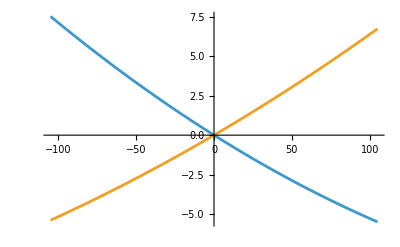

```mathematica
list={{-105,0.000059854097266348784,0.00007397891883424507},{-95,0.00005985361547970964,0.0000739792564146857},{-85,0.000059853144705296395,0.00007397960304631872},{-75,0.00005985268494315609,0.00007397995872906343},{-65,0.00005985223619335577,0.00007398032346283694},{-55,0.00005985179845595269,0.0000739806972475607},{-45,0.00005985137173104522,0.00007398108008314915},{-35,0.000059850956018714806,0.00007398147196952242},{-25,0.00005985055131903885,0.0000739818729066038},{-15,0.000059850157632079805,0.0000739822828943218},{-5,0.000059849774957960084,0.00007398270193259397},{0,0.00005984958775070338,0.00007398291484567346},{5,0.00005984940329666769,0.00007398313002136913},{15,0.00005984904264846814,0.00007398356716053793},{25,0.00005984869301331649,0.00007398401335006056},{35,0.00005984835439134071,0.00007398446858986152},{45,0.000059848026782637835,0.00007398493287987444},{55,0.000059847710187309715,0.0000739854062200337},{65,0.00005984740460547817,0.00007398588861027154},{75,0.00005984711003718835,0.00007398638005053895},{85,0.00005984682648259741,0.00007398688054076455},{95,0.00005984655394181104,0.00007398739008089035},{105,0.000059846292414923556,0.00007398790867086285}};
len=Length[list];
x=1/0.00005984958775070338;
d1at21=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^5},{i,1,len}];
x=1/0.00007398291484567346;
d1at22=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^5},{i,1,len}];
ListLinePlot[{d1at21,d1at22}]
```

```mathematica
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[sign[B,mu,cval,v0val,{in,2 in}, bohrrm,omval],{B,-105,105,10}]
```

```mathematica
Quiet[sign[0.01,mu,cval,v0val,{in,2in}, bohrrm,omval]]//Chop
```

{0.01,0.0000346307,0.0000459486}

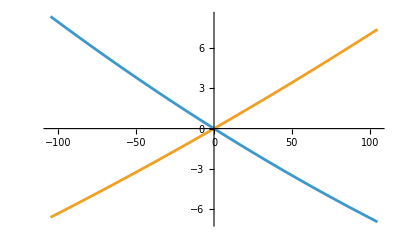

```mathematica
list={{-105,0.00003463357765973437,0.00004594555834919322},{-95,0.00003463327990950717,0.0000459458333799124},{-85,0.000034632986583756995,0.00004594611168090683},{-75,0.00003463269768248369,0.00004594639325213949},{-65,0.000034632413205772424,0.000045946678093550904},{-55,0.00003463213315362806,0.00004594696620510514},{-45,0.000034631857526136445,0.00004594725758674481},{-35,0.00003463158632328794,0.00004594755223844029},{-25,0.000034631319545170856,0.000045947850160135994},{-15,0.00003463105719178222,0.0000459481513518028},{-5,0.00003463079926328876,0.000045948455813365664},{0,0.000034630671958311244,0.00004594860927036787},{5,0.00003463054575949944,0.00004594876354485},{15,0.000034630296680828856,0.000045949074546114416},{25,0.00003463005202702979,0.00004594938881720223},{35,0.00003462981179826385,0.00004594970635804453},{45,0.00003462957599455854,0.000045950027168610866},{55,0.000034629344616004376,0.00004595035124885438},{65,0.00003462911766266174,0.00004595067859873782},{75,0.00003462889513452342,0.000045951009218243906},{85,0.00003462867703172674,0.00004595134310731628},{95,0.000034628463354294584,0.000045951680265931673},{105,0.00003462825410229797,0.00004595202069405457}};
len=Length[list];
x=1/0.000034630671958311244;
d1at31=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^5},{i,1,len}];
x=1/0.00004594860958592459;
d1at32=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^5},{i,1,len}];
ListLinePlot[{d1at31,d1at32}]
```

```mathematica
mu=10.0^0; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[sign[B,mu,cval,v0val,{in,50in}, bohrrm,omval],{B,-105,105,10}]
```

```mathematica
Quiet[sign[0.01,mu,cval,v0val,{in,50in}, bohrrm,omval]]//Chop
```

{0.01,1.59777×10^-6,2.42479×10^-6}

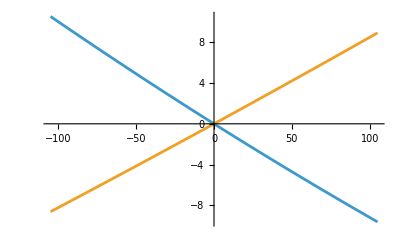

```mathematica
list={{-105,1.5979381045131573*^-6,2.4245816346727713*^-6},{-95,1.5979214699453394*^-6,2.4246012173521304*^-6},{-85,1.597904966884313*^-6,2.4246208649351323*^-6},{-75,1.5978885953315344*^-6,2.424640577419767*^-6},{-65,1.5978723552908999*^-6,2.424660354803153*^-6},{-55,1.5978562467626588*^-6,2.424680197083831*^-6},{-45,1.5978402697507573*^-6,2.424700104258988*^-6},{-35,1.597824424257452*^-6,2.424720076326494*^-6},{-25,1.597808710285791*^-6,2.424740113283966*^-6},{-15,1.5977931278363082*^-6,2.4247602151300164*^-6},{-5,1.5977776769184123*^-6,2.4247803818599446*^-6},{0,1.5977700007754203*^-6,2.424790489559188*^-6},{5,1.597762357518797*^-6,2.424800613477686*^-6},{15,1.5977471696577824*^-6,2.424820909974504*^-6},{25,1.5977321133311957*^-6,2.424841271350972*^-6},{35,1.5977171885406106*^-6,2.4248616976055258*^-6},{45,1.5977023952915308*^-6,2.4248821887351717*^-6},{55,1.5976877335852903*^-6,2.4249027447385306*^-6},{65,1.5976732034248004*^-6,2.4249233656136697*^-6},{75,1.5976588048143947*^-6,2.4249440513581726*^-6},{85,1.5976445377552254*^-6,2.4249648019708583*^-6},{95,1.5976304022518362*^-6,2.4249856174493166*^-6},{105,1.5976163983078123*^-6,2.425006497791542*^-6}};
len=Length[list];
dat1=Table[{list[[i,1]],Re[list[[i,2]]]},{i,1,len}];
dat2=Table[{list[[i,1]],Re[list[[i,3]]]},{i,1,len}];
x=1/1.5977700007754203*^-6;
d1at41=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^5},{i,1,len}];
x=1/2.424790489559188*^-6;
d1at42=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^5},{i,1,len}];
ListLinePlot[{d1at41,d1at42}]
```

### set 2

```mathematica
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[sign[B,mu,cval,v0val,{in,0.5in}, bohrrm,omval],{B,-105,105,10}]
```

```mathematica
Quiet[sign[0.01,mu,cval,v0val,{in,0.5in}, bohrrm,omval]]//Chop
```

{0.01,7.90244×10^-6,0.0000123476}

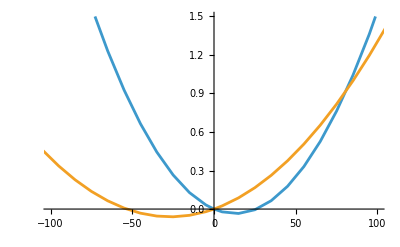

```mathematica
list={{-105,7.925045444092265*^-6,0.000012353242783485429},{-95,7.92133171891594*^-6,0.00001235170533213081},{-85,7.91794662041635*^-6,0.000012350377692403911},{-75,7.91489012013965*^-6,0.000012349259840904235},{-65,7.912162195145012*^-6,0.000012348351755678505},{-55,7.909762828000562*^-6,0.000012347653416220091},{-45,7.907692006784409*^-6,0.000012347164803467887},{-35,7.90594972508147*^-6,0.000012346885899805674},{-25,7.904535981985595*^-6,0.000012346816689061174},{-15,7.90345078209625*^-6,0.000012346957156505862},{-5,7.902694135519732*^-6,0.000012347307288854273},{0,7.902439024390243*^-6,0.000012347560975609756},{5,7.902266057876282*^-6,0.000012347867074262494},{15,7.902166570291282*^-6,0.000012348636502329375},{25,7.902395699405767*^-6,0.000012349615564094855},{35,7.902953477378367*^-6,0.00001235080425203954},{45,7.90383994188454*^-6,0.000012352202560085248},{55,7.905055136123226*^-6,0.000012353810483594165},{65,7.906599108820888*^-6,0.000012355628019368808},{75,7.908471914236454*^-6,0.000012357655165651764},{85,7.910673612167333*^-6,0.00001235989192212572},{95,7.913204267954267*^-6,0.000012362338289913375},{105,7.916063952488436*^-6,0.000012364994271577667}};
len=Length[list];
x=1/7.902439024390243*^-6;
d2at11=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^3},{i,1,len}];
x=1/0.000012347560975609756;
d2at12=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^3},{i,1,len}];
ListLinePlot[{d2at11,d2at12},PlotRange->{{-100,100},{-0.1,1.5}}]
```

```mathematica
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[sign[B,mu,cval,v0val,{in, in}, bohrrm,omval],{B,-105,105,10}]
```

```mathematica
Quiet[sign[0.01,mu,cval,v0val,{in,in}, bohrrm,omval]]//Chop
```

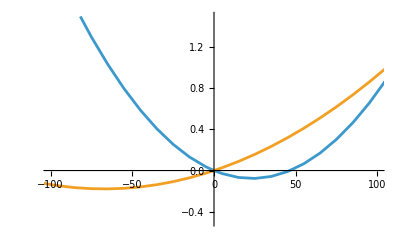

```mathematica
list={{-105,4.7007127186549635*^-6,9.134066224403095*^-6},{-95,4.6990629590606785*^-6,9.133829720661486*^-6},{-85,4.6975470773560095*^-6,9.133665522252361*^-6},{-75,4.69616505301042*^-6,9.133573614734039*^-6},{-65,4.694916869027013*^-6,9.13355398466828*^-6},{-55,4.693802511940194*^-6,9.13360661961982*^-6},{-45,4.692821971815342*^-6,9.133731508155633*^-6},{-35,4.691975242247335*^-6,9.133928639844345*^-6},{-25,4.6912623203620956*^-6,9.13419800525535*^-6},{-15,4.690683206813949*^-6,9.134539595958877*^-6},{-5,4.690237905785666*^-6,9.13495340452564*^-6},{0,4.690065437239738*^-6,9.135187388459248*^-6},{5,4.689926424993382*^-6,9.13543942452536*^-6},{15,4.6897487756818935*^-6,9.135997650527828*^-6},{25,4.689704972631155*^-6,9.136628078101383*^-6},{35,4.689795034154237*^-6,9.137330703813511*^-6},{45,4.690018982101677*^-6,9.138105525230126*^-6},{55,4.690376841862929*^-6,9.138952540915647*^-6},{65,4.690868642369479*^-6,9.139871750432795*^-6},{75,4.691494416098158*^-6,9.140863154342466*^-6},{85,4.692254199075164*^-6,9.141926754203692*^-6},{95,4.693148030878691*^-6,9.143062552573808*^-6},{105,4.694175954644215*^-6,9.144270553008483*^-6}};
len=Length[list];
x=1/4.690065437239738*^-6;
d2at21=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^3},{i,1,len}];
x=1/9.135187388459248*^-6;
d2at22=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^3},{i,1,len}];
ListLinePlot[{d2at21,d2at22},PlotRange->{{-100,100},{-0.5,1.5}}]
```

```mathematica
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[sign[B,mu,cval,v0val,{in,2 in}, bohrrm,omval],{B,-105,105,10}]
```

```mathematica
sign[0.01,mu,cval,v0val,{in,2 in}, bohrrm,omval]
```

{0.01,2.49111×10^-6,6.08181×10^-6}

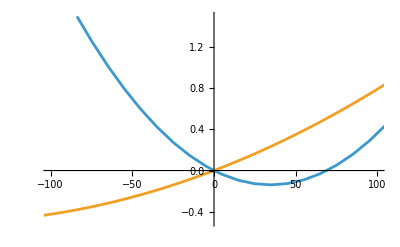

```mathematica
list={{-105,2.4964366341662074*^-6,6.079148550649042*^-6},{-95,2.4956524596204293*^-6,6.079296262286952*^-6},{-85,2.4949265968961345*^-6,6.079466290175374*^-6},{-75,2.4942590348375083*^-6,6.079658626905559*^-6},{-65,2.4936497642379585*^-6,6.07987326556036*^-6},{-55,2.493098777838846*^-6,6.080110199713923*^-6},{-45,2.492606070328732*^-6,6.080369423431339*^-6},{-35,2.4921716383433497*^-6,6.08065093126801*^-6},{-25,2.4917954804651652*^-6,6.080954718269443*^-6},{-15,2.491477597222534*^-6,6.081280779971129*^-6},{-5,2.4912179910924067*^-6,6.081629112397403*^-6},{0,2.491110043248439*^-6,6.081811629024508*^-6},{5,2.4910166664949354*^-6,6.0819997120631516*^-6},{15,2.49087362980014*^-6,6.082392575971477*^-6},{25,2.4907888893286896*^-6,6.0828077016135436*^-6},{35,2.490762455347838*^-6,6.08324508697008*^-6},{45,2.49079434007598*^-6,6.0837047305101365*^-6},{55,2.4908845576841544*^-6,6.084186631190934*^-6},{65,2.4910331242966778*^-6,6.084690788458135*^-6},{75,2.4912400579940778*^-6,6.08521720224539*^-6},{85,2.491505378814387*^-6,6.085765872974675*^-6},{95,2.491829108755654*^-6,6.08633680155609*^-6},{105,2.4922112717785613*^-6,6.086929989388016*^-6}};
len=Length[list];
x=1/2.491110043248439*^-6;
d2at31=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^3},{i,1,len}];
x=1/6.081811629024508*^-6;
d2at32=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^3},{i,1,len}];
ListLinePlot[{d2at31,d2at32},PlotRange->{{-100,100},{-0.5,1.5}}]
```

```mathematica
mu=10.0^-1; cval=5 10^-5 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[sign[B,mu,cval,v0val,{in,50in}, bohrrm,omval],{B,-105,105,10}]
```

```mathematica
sign[0.01,mu,cval,v0val,{in,50in}, bohrrm,omval]
```

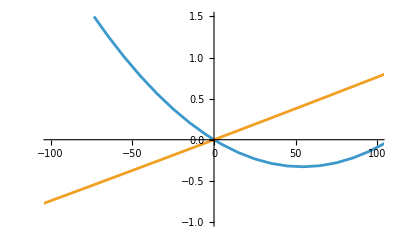

```mathematica
list={{-105,9.430983789193766*^-8,3.649836321659453*^-7},{-95,9.427727000790104*^-8,3.650104464873855*^-7},{-85,9.424681542271685*^-8,3.650373328932835*^-7},{-75,9.421847373251246*^-8,3.650642912080817*^-7},{-65,9.419224461591666*^-8,3.650913212631092*^-7},{-55,9.416812783400616*^-8,3.651184228965648*^-7},{-45,9.414612323025055*^-8,3.6514559595351067*^-7},{-35,9.412623073053236*^-8,3.651728402858249*^-7},{-25,9.410845034312251*^-8,3.6520015575219394*^-7},{-15,9.40927821586349*^-8,3.6522754221811387*^-7},{-5,9.407922635010772*^-8,3.652549995558374*^-7},{0,9.407324066344862*^-8,3.652687547635465*^-7},{5,9.406778317299708*^-8,3.6528252764437074*^-7},{15,9.405845296510403*^-8,3.6531012636950935*^-7},{25,9.405123614679077*^-8,3.6533779562373765*^-7},{35,9.404613322090781*^-8,3.65365535306275*^-7},{45,9.404314477289809*^-8,3.653933453230434*^-7},{55,9.404227147084325*^-8,3.654212255866695*^-7},{65,9.404351406554585*^-8,3.6544917601647316*^-7},{75,9.404687339065934*^-8,3.654771965384385*^-7},{85,9.40523503627371*^-8,3.655052870852382*^-7},{95,9.405994598137217*^-8,3.6553344759620444*^-7},{105,9.406966132931663*^-8,3.655616780173348*^-7}};
len=Length[list];
x=1/9.407324066344862*^-8;
d2at41=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^3},{i,1,len}];
x=1/3.652687547635465*^-7;
d2at42=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^3},{i,1,len}];
ListLinePlot[{d2at41,d2at42},PlotRange->{{-100,100},{-1,1.5}}]
```

### set3

```mathematica
mu=10.0^-1; cval=5 10^-4 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[Quiet[sign[B,mu,cval,v0val,{in,0.5in}, bohrrm,omval]]//Chop,{B,-105,105,10}]
```

```mathematica
Quiet[sign[0.01,mu,cval,v0val,{in,0.5in}, bohrrm,omval]]//Chop
```

{0.01,0.0000930583,0.000107192}

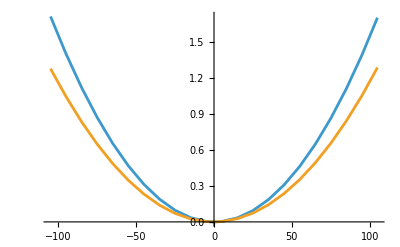

```mathematica
list=Sort[{{-105,0.00010899846596465414,0.00012088389738933464},{-95,0.00010608359284663076,0.00011837713029213649},{-85,0.00010347038365574817,0.00011612853670163613},{-75,0.00010115535235307578,0.00011413586293662978},{-65,0.00009913546751078534,0.00011239713611699813},{-55,0.0000974081276519236,0.00011091065238327058},{-45,0.00009597114067917319,0.0001096749669386419},{-35,0.00009482270695945175,0.00010868888576005405},{-25,0.00009396140572031874,0.00010795145885419104},{-15,0.00009338618448976831,0.00010746197495957899},{-5,0.00009309635137604423,0.00010721995761863854},{0,0.00009305833645251493,0.000107191663547485},{5,0.00009309157004160984,0.00010722516256405601},{15,0.00009337185727760261,0.00010747757638283502},{25,0.00009393758313400939,0.00010797741643940123},{35,0.00009478947360793669,0.00010872513205667058},{45,0.0000959286159397977,0.00010972140697146761},{55,0.00009735646661625346,0.00011096716309862557},{65,0.00009907486223144566,0.00011246356565693577},{75,0.00010108603341621828,0.00011421202973041546},{85,0.00010339262211099465,0.00011621422836071874},{95,0.00010599770253480212,0.00011847210229146934},{105,0.00010890480629371078,0.00012098787151402254}}];
len=Length[list];
x=1/0.00009305833645251493;
d3at11=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^1},{i,1,len}];
x=1/0.000107191663547485;
d3at12=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^1},{i,1,len}];
ListLinePlot[{d3at11,d3at12}]
```

```mathematica
mu=10.0^-1; cval=5 10^-4 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[Quiet[sign[B,mu,cval,v0val,{in,in}, bohrrm,omval]]//Chop,{B,-105,105,10}]
```

```mathematica
Quiet[sign[75,mu,cval,v0val,{in,in}, bohrrm,omval]]//Chop
```

{75,0.0000628601,0.0000766672}

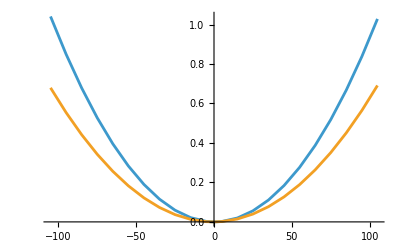

```mathematica
list=Sort[{{-105,0.00006607890627409653,0.00007900898402905443},{-95,0.0000649338534202588,0.00007808094881456963},{-85,0.00006391004517763555,0.00007725090771494304},{-75,0.00006300515031586315,0.00007651731711769251},{-65,0.00006221714449195913,0.00007587882830582045},{-55,0.00006154429257302748,0.00007533427851493985},{-45,0.00006098513389599452,0.00007488268337963111},{-35,0.00006053847015085679,0.0000745232306504588},{-25,0.000060203355638426876,0.00007425527508552918},{-15,0.00005997908970830565,0.00007407833444024745},{-5,0.00005986521122985436,0.00007399208649640075},{0,0.00005984958775070341,0.00007398291484567347},{5,0.00005986149499057578,0.00007399636708758684},{15,0.00005996794995406211,0.00007409116909270691},{25,0.00006018481934498431,0.00007427664238318344},{35,0.000060512582562778975,0.00007455309472311687},{45,0.00006095195895990332,0.00007492099363513265},{55,0.00006150391355603094,0.00007538096925854688},{65,0.00006216966479763396,0.00007593381824106215},{75,0.00006295069451446587,0.00007658050872094773},{85,0.00006384876027216535,0.00007732218647389586},{95,0.00006486591037577276,0.00007816018231824355},{105,0.00006600450184460156,0.00007909602089432717}}];
len=Length[list];
x=1/0.00005984958775070341;
d3at21=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^1},{i,1,len}];
x=1/0.00007398291484567347;
d3at22=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^1},{i,1,len}];
ListLinePlot[{d3at21,d3at22}]
```

```mathematica
mu=10.0^-1; cval=5 10^-4 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[Quiet[sign[B,mu,cval,v0val,{in,2in}, bohrrm,omval]]//Chop,{B,-105,105,10}]
```

```mathematica
Quiet[sign[0.01,mu,cval,v0val,{in,2in}, bohrrm,omval]]//Chop
```

{0.01,0.0000346307,0.0000459486}

```mathematica
list=Sort[{{-105,0.0000371615585108222,0.00004776194506551197},{-95,0.00003669465802574599,0.000047423623030255353},{-85,0.00003627810213768134,0.000047121977443044375},{-75,0.00003591060390667363,0.00004685618193650128},{-65,0.00003559104897526354,0.00004662551687392384},{-55,0.00003531848460156272,0.00004642936364828423},{-45,0.000035092110527978814,0.000046267199877460146},{-35,0.0000349112714849419,0.00004613859541551053},{-25,0.000034775451170418305,0.00004604320911505713},{-15,0.000034684267580956425,0.00004598078628924683},{-5,0.000034637469600194546,0.00004595115683359122},{0,0.000034630671958311244,0.000045948609270367876},{5,0.000034634934777333685,0.00004595423397872595},{15,0.00003467666825223148,0.00004599001365504522},{25,0.00003476280280626985,0.00004605857445958589},{35,0.00003489360004003994,0.000046160078224648335},{45,0.00003506945270065288,0.00004629477119678974},{55,0.000035290888204205534,0.0000464629858441683},{65,0.000035558573423216395,0.00004666514332007454},{75,0.00003587332083572468,0.0000469017566211232},{85,0.0000362360961633171,0.00004717343449025722},{95,0.00003664802766083123,0.00004748088612794363},{105,0.000037110417262616686,0.00004782492678994826}}];
len=Length[list];
x=1/0.000034630671958311244;
d3at31=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^1},{i,1,len}];
x=1/0.000045948609270367876;
d3at32=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^1},{i,1,len}];
ListLinePlot[{d3at21,d3at22}]
```

-Graphics-

```mathematica
mu=10.0^-1; cval=5 10^-4 ;v0val= 5 10^-4; omval=1 ; bohrrm=3*10^-7 ;in=1;
dat=Table[Quiet[sign[B,mu,cval,v0val,{in,50in}, bohrrm,omval]]//Chop,{B,-105,105,10}]
```

{{-105,1.6744×10^-6,2.45979×10^-6},{-95,1.66024×10^-6,2.45304×10^-6},{-85,1.64764×10^-6,2.44708×10^-6},{-75,1.63654×10^-6,2.44186×10^-6},{-65,1.6269×10^-6,2.43737×10^-6},{-55,1.61868×10^-6,2.43358×10^-6},{-45,1.61185×10^-6,2.43049×10^-6},{-35,1.60639×10^-6,2.42807×10^-6},{-25,1.60227×10^-6,2.42631×10^-6},{-15,1.59948×10^-6,2.42522×10^-6},{-5,1.59801×10^-6,2.42477×10^-6},{5,1.59786×10^-6,2.42497×10^-6},{15,1.59902×10^-6,2.42582×10^-6},{25,1.6015×10^-6,2.42732×10^-6},{35,1.60532×10^-6,2.42948×10^-6},{45,1.61048×10^-6,2.4323×10^-6},{55,1.61701×10^-6,2.4358×10^-6},{65,1.62493×10^-6,2.43998×10^-6},{75,1.63428×10^-6,2.44486×10^-6},{85,1.64509×10^-6,2.45047×10^-6},{95,1.65741×10^-6,2.45682×10^-6},{105,1.6713×10^-6,2.46395×10^-6}}

```mathematica
Quiet[sign[0.01,mu,cval,v0val,{in,50in}, bohrrm,omval]]//Chop
```

{0.01,1.59777×10^-6,2.42479×10^-6}

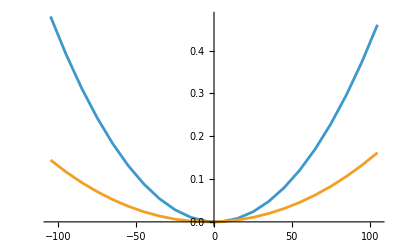

```mathematica
list=Sort[{{-105,1.674401109677899*^-6,2.4597883881900077*^-6},{-95,1.660241880606601*^-6,2.4530428919945157*^-6},{-85,1.647637910116483*^-6,2.4470750234723237*^-6},{-75,1.6365377678896707*^-6,2.4418574111983205*^-6},{-65,1.6268971909535537*^-6,2.437366440862476*^-6},{-55,1.6186785430247724*^-6,2.4335819785995726*^-6},{-45,1.611850366247152*^-6,2.4304871393601397*^-6},{-35,1.6063870145860724*^-6,2.4280680957320098*^-6},{-25,1.6022683603760647*^-6,2.426313923509364*^-6},{-15,1.5994795673967276*^-6,2.4252164810815435*^-6},{-5,1.5980109254691405*^-6,2.424770320392046*^-6},{0,1.5977700007754208*^-6,2.4247904895591876*^-6},{5,1.5978577429837684*^-6,2.4249726278306467*^-6},{15,1.599020295053792*^-6,2.4258231939848265*^-6},{25,1.6015038261895102*^-6,2.4273244117064036*^-6},{35,1.6053186075420007*^-6,2.4294813024660413*^-6},{45,1.6104800499271021*^-6,2.432301571481378*^-6},{55,1.6170088750428112*^-6,2.435795692633737*^-6},{65,1.6249313485876214*^-6,2.4399770247469382*^-6},{75,1.634279580420625*^-6,2.444861961408493*^-6},{85,1.6450918985414594*^-6,2.4504701171834135*^-6},{95,1.6574133055731958*^-6,2.4568245538358855*^-6},{105,1.6712960287017621*^-6,2.4639520510478246*^-6}}];
len=Length[list];
x=1/1.5977700007754208*^-6;
d3at41=Table[{list[[i,1]],(Re[list[[i,2]]]x-1)10^1},{i,1,len}];
x=1/2.4247904895591876*^-6;
d3at42=Table[{list[[i,1]],(Re[list[[i,3]]]x-1)10^1},{i,1,len}];
ListLinePlot[{d3at41,d3at42}]
```

## Plots

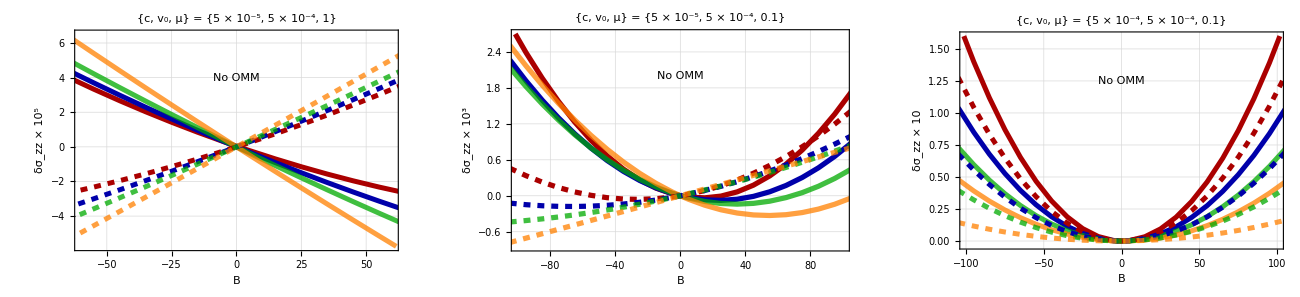

```mathematica
style={(**)Directive[Darker[Red],Thickness[0.008]],(**)Directive[Darker[Blue],Thickness[0.008]],Directive[Darker[Green],Thickness[0.008],Opacity[0.75]],(**)Directive[Orange,Thickness[0.008],Opacity[0.75]](*********),Directive[Darker[Red],Thickness[0.008],Dashed],(**)Directive[Darker[Blue],Thickness[0.008],Dashed],Directive[Darker[Green],Thickness[0.008],Opacity[0.75],Dashed],(**)Directive[Orange,Thickness[0.008],Opacity[0.75],Dashed]};

g1=ListPlot[{d1at11,d1at21,d1at31,d1at41,d1at12,d1at22,d1at32,d1at42},Joined->True,(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-60,60},{-5.75,6.5}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10^5"},PlotLabel->Style["{c, v_0, μ} = {5 × 10^-5,  5 × 10^-4, 1}",Bold,Darker[Brown],18],ImageSize->450,GridLines->Automatic,(*****)Epilog->{Style[Text["No OMM",{0,4}],Blue,16,Bold]}(*******)];

g2=ListLinePlot[{d2at11,d2at21,d2at31,d2at41,d2at12,d2at22,d2at32,d2at42},(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},{-0.85,2.7}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10^3"},PlotLabel->Style["{c, v_0, μ} = {5 × 10^-5,  5 × 10^-4, 0.1}",Bold,Darker[Brown],18],ImageSize->470,GridLines->Automatic,Epilog->{Style[Text["No OMM",{0,2}],Blue,16,Bold]}];

g3=ListLinePlot[{d3at11,d3at21,d3at31,d3at41,d3at12,d3at22,d3at32,d3at42},(*********)FrameTicksStyle->Directive[Darker[Gray],16],PlotRange->{{-100,100},{-0.03,1.6}},LabelStyle->{Black,Bold,22},PlotStyle->style,Frame->True,Axes->False,FrameLabel->{"B","δσ_zz × 10"},PlotLabel->Style["{c, v_0, μ} = {5 × 10^-4,  5 × 10^-4, 0.1}",Bold,Darker[Brown],18],ImageSize->450,GridLines->Automatic,Epilog->{Style[Text["No OMM",{0,1.25}],Blue,16,Bold]}];


leg=LineLegend[style,{"1, 0.5","1, 1","1, 2","1, 50","-1, 0.5","-1, 1","-1, 2","-1, 50"},LabelStyle->{18,Darker[Brown],Bold},LegendLayout->{"Row",1}];

pl=Legended[GraphicsGrid[{{g1,g2,g3}},Spacings->{20,0},ImageSize->1300],Placed[leg,Below]]
SetDirectory[NotebookDirectory[]];
Export["allnoomm.pdf",Rasterize[pl],ImageResolution->1000];
```